```mathematica
IntegerString[Distance[FromDigits["111111111111111111112",3],3],3]
```

111111111111111111111

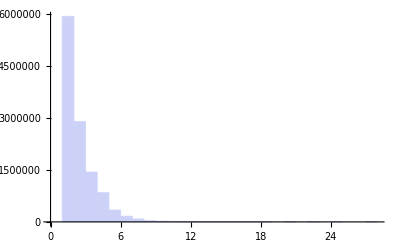
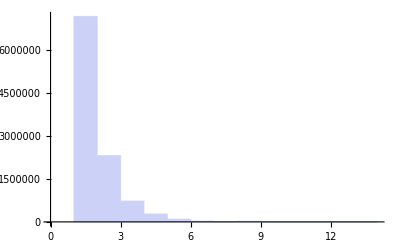
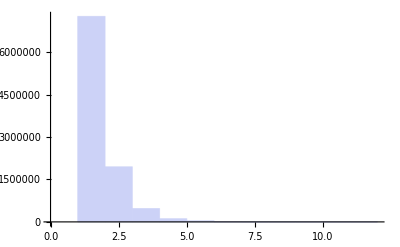

```mathematica
With[
{tuple={3,5,7}},
With[{values=ReadList[FileNameForTuple[tuple],Number,100000]},
Table[
Histogram[
Flatten[
Table[Map[Length,Split[IntegerDigits[v,p]]],{v,values}]
]]
,{p,tuple}]
]
]
```

```mathematica
TableForm[With[
{tuple={3,5,7}},
With[{values=ReadList[FileNameForTuple[tuple],Number,100]},
Table[{IntegerDigits[v,3],Map[Length,Split[IntegerDigits[v,3]]]},{v,values}]
]
],TableDepth->1
]
```

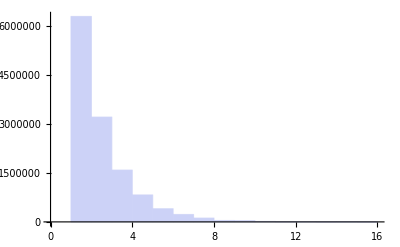
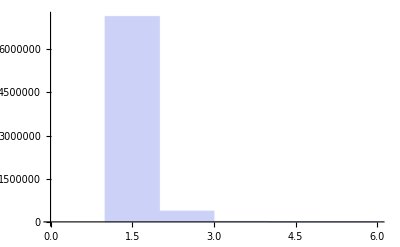
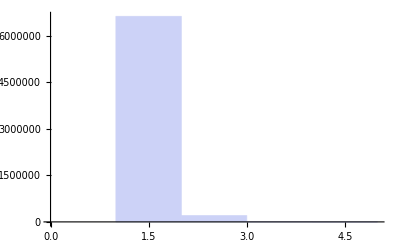
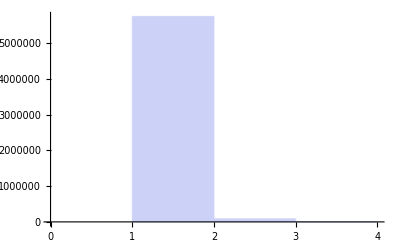
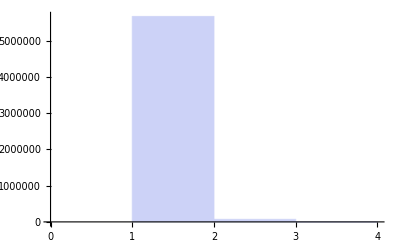

```mathematica
With[
{tuple={3,37,59,127,139}},
With[{values=ReadList[FileNameForTupleBis[tuple],Number,10000]},
Table[
Histogram[
Flatten[
Table[Map[Length,Split[IntegerDigits[v,p]]],{v,values}]
]]
,{p,tuple}]
]
]
```

```mathematica
Length[ReadList[FileNameForTupleBis[{3,37,59,127,139}]]]
```

32267

OK

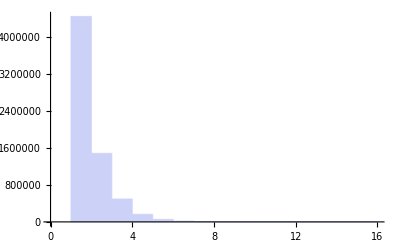

```mathematica
With[
{tuple={3,37,59,127,139}},
With[{values=Table[RandomInteger[{1,3^10000}],{v,1,1000}]},
Print["OK"];
Monitor[
Table[
Histogram[
Flatten[
Table[Map[Length,Split[IntegerDigits[values[[i]],p]]],{i,1,Length[values]}]
]]
,{p,{3}}]
,{i,p}
]
]
]
```

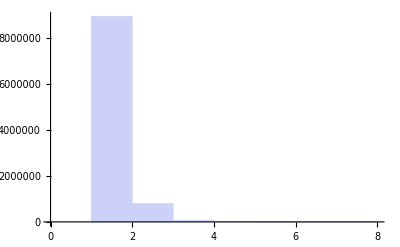

```mathematica
With[
{tuple={3,5,7}},
With[{values=ReadList[FileNameForTuple[tuple],Number,100000]},
Table[
Histogram[
Flatten[
Table[Map[Length,Split[IntegerDigits[v,p]]],{v,values}]
]]
,{p,{11}}]
]
]
```